```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*graphDataMany*)
```

```mathematica
data =Partition[ReadList["./graphDataMany.txt", Real], 2];
min = data[[1]][[2]];
minTau = data[[1]][[1]];
index = 1;
For[i = 1, i < Length[data], ++i, 

If[data[[i]][[2]] < min, 
min = data[[i]][[2]];
minTau = data[[i]][[1]];
index = i;
]
]
```

```mathematica
minPoint = {minTau, min}
```

{0.03528,27.}

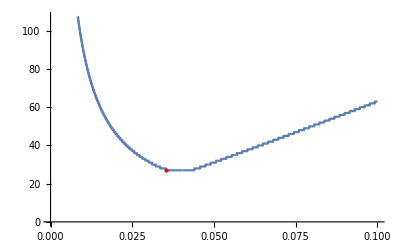

```mathematica
ListLinePlot[{data}, Epilog->{Red,PointSize@Large,Point[minPoint]}]
```